```mathematica
ClearAll["Global`*"]
```

## Common

```mathematica
RestylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]];
```

```mathematica
dashingStyle = Dashing[{maxt/2,maxt/2-maxt/10}];
```

```mathematica
pathToOutput=ToString["\..\plots\ideal-integr\\"];
```

```mathematica
sizeText[text_]:=Text@TraditionalForm@Style[text, 18,Plain,FontFamily->"Times"];
```

## Step response

### TF function

```mathematica
k=10;
maxt = 0.04;
TFsimple=k /s;
TF=TransferFunctionModel[TFsimple,s];
TFstep=Simplify[OutputResponse[TF,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

### Plot

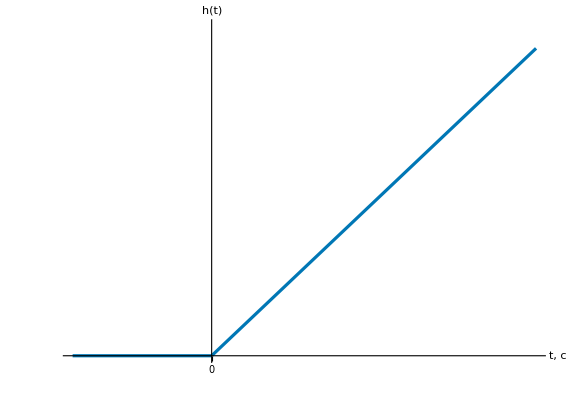

```mathematica
tickXStep=1/100;
tickYStep=0.1;

stepRespPic=Plot[{TFstep}, {t, -0.3*maxt, maxt-0.3*maxt},
LabelStyle->{FontFamily->"Arial",14,Black},
AxesLabel->{sizeText["t, с"],sizeText["h(t)"]},
AxesStyle->Directive[Thickness[0.002],Black],
GridLines->None,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{-0.3*maxt,maxt-0.3*maxt},{0,0.3}},
PlotRangeClipping->False,
AspectRatio->11/16,
ImageSize->Large,
Ticks->{
Prepend[(#&@Array[{tickXStep#,,{0.01,0}}&,100]),{0,0}],
(#&@Array[{tickYStep#,,{0.01,0}}&,100])
}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"step.svg";
Export[fName,stepRespPic];
```

## Bode plot

### Approx

```mathematica
tfm=TFsimple;
minF=Log10[10];
maxF=Log10[1000];
cF1=Log10[100];
xcoords={minF,cF1,maxF};
mag0=20 Log10@Abs[tfm/.s->I 0.001];
ls={mag0,0,-20 (maxF-cF1)};
ycoords=FoldList[Plus,ls[[1]],ls[[2;;-1]]];
```

### Vert Line

```mathematica
wLine=Line[{
{cF1,mag0},
{cF1,0}
}];
```

### Log Plot

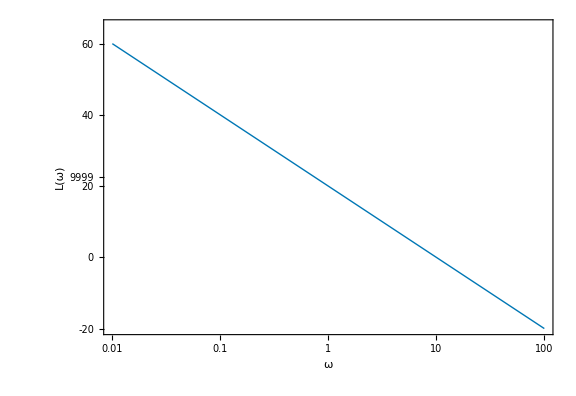

```mathematica
bodePlot=BodePlot[TF,{0.01,10^2},PlotRange->{{-20,65},Automatic},
PlotStyle->Thickness[0.004],
ImageSize->Large,
AxesStyle->Directive[Thickness[0.002],Black]
];
ampBodePlot=RestylePlot[
bodePlot[[1,1,1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
AxesStyle->Directive[Thickness[0.002],Black],
LabelStyle->{
FontFamily->"Arial",14,Black
},
AspectRatio->11/16,
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-apm-freq.svg";
Export[fName,ampBodePlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\ideal-integr\log-apm-freq.svg

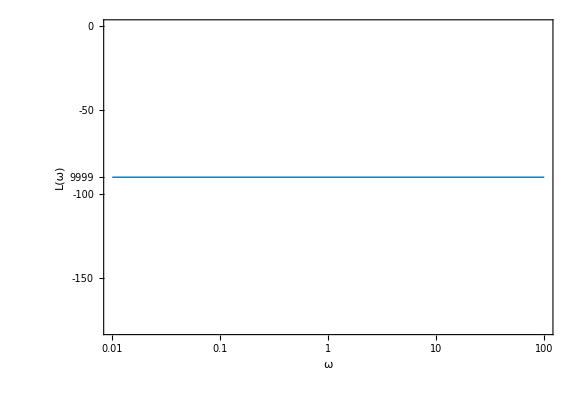

```mathematica
phaseBodePlot=RestylePlot[
bodePlot[[1,2,1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
AspectRatio->11/16,
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-phase-freq.svg";
Export[fName,phaseBodePlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\ideal-integr\log-phase-freq.svg

### Plot

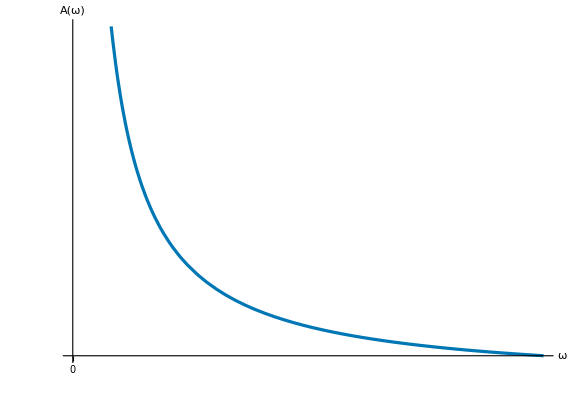

```mathematica
ampPlot=Plot[Abs[TF[I f]], {f, 0, 100},
(*PlotRange->{{0,Full},{0,10}},*)
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["A(ω)"]},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
LabelStyle->{
FontFamily->"Arial",14,Black
},
Ticks->{
Prepend[(#&@Array[{10#,,{0.01,0}}&,100]),{0,0}],
(#&@Array[{0.1#,,{0.01,0}}&,100])
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{0, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"amp-freq.svg";
Export[fName,ampPlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\ideal-integr\amp-freq.svg

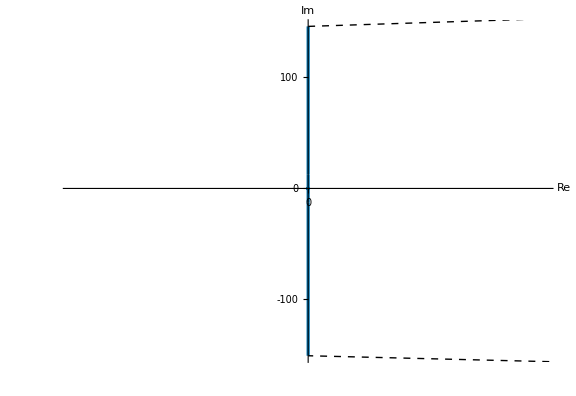

```mathematica
nyquistPlot=NyquistPlot[TF,
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["Re"],sizeText["Im"]},
AxesOrigin->{0,0},
AspectRatio->11/16,
AxesStyle->Directive[Thickness[0.002],Black],
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"nyquist.svg";
Export[fName,nyquistPlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\ideal-integr\nyquist.svg